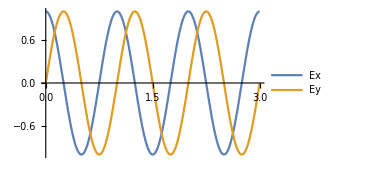

```mathematica
Plot[{Cos[2π t],Cos[2 π t-π/2]},{t,0,3},PlotLegends->{"Ex","Ey"}]
```

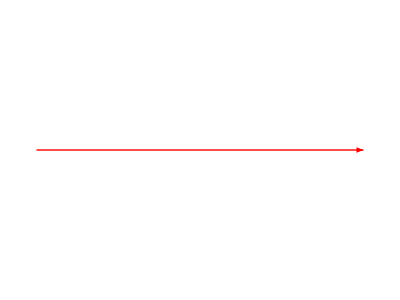
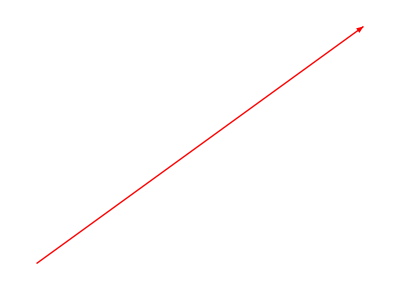
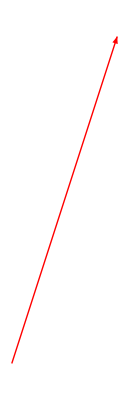
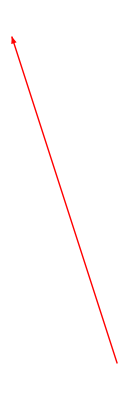
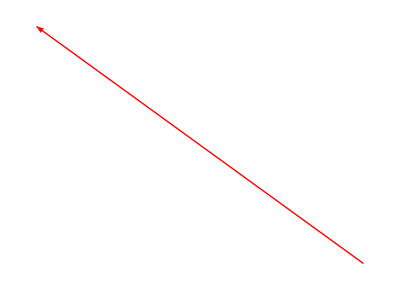
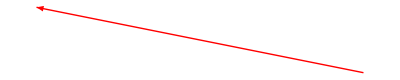
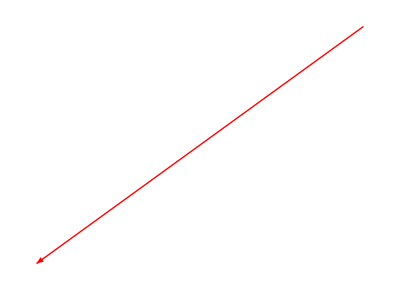
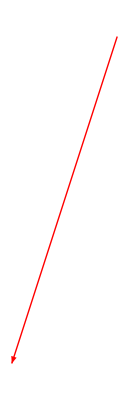

```mathematica
Ex =Cos[2π t];Ey=Cos[2 π t-π/2];
Table[Show[Graphics[{Red,Arrow[{{0,0},{Ex,Ey}}]}]],{t,Range[0,1,0.1]}]
```